## Дистиллят 1 л. В таблице: 1 - напряжение между электродами в В, 2 - ток в мА, 3 -напряжение у + в В, 4 - напряжение у - в В

```mathematica
data1 = {{0,0,0,0},{1,0.001,0.46,0.2},{2,0.0013,0.9,0.39},{3,0.0026,1.5,0.5},{4,0.004,2.2,0.65},{5,0.006,2.9,0.8}};
```

## Дистиллят 1 л + 1 г Na2SO4. В таблице: 1 - напряжение между электродами в В, 2 - ток в мА, 3 -напряжение у + в В, 4 - напряжение у - в В

```mathematica
data2 = {{0,0,0,0},{1,0.002, 0.42, 0.25},{2,0.017, 0.6, 0.56},{3,0.114, 1.3, 1.13},{4,0.525, 2.2, 1.35},{5,0.95, 3.03, 1.53}};
```

## Дистиллят 1 л + 2 г Na2SO4. В таблице: 1 - напряжение между электродами в В, 2 - ток в мА, 3 -напряжение у + в В, 4 - напряжение у - в В

```mathematica
data3 = {{0,0,0,0},{1,0.001, 0.22, 0.24},{2,0.015, 0.59, 0.56},{3,0.303, 1.42, 1.12},{4,1.013, 2.2, 1.41},{5,1.805, 2.92, 1.6}};
```

## Дистиллят 1 л + 3 г Na2SO4. В таблице: 1 - напряжение между электродами в В, 2 - ток в мА, 3 -напряжение у + в В, 4 - напряжение у - в В

```mathematica
data4 = {{0,0,0,0},{1,0.0006, 0.23, 0.23},{2,0.015, 0.56, 0.54},{3,0.355, 1.37, 1.16},{4,1.25, 2.15, 1.33},{5,2.53, 3.13, 1.53}};
```

## Дистиллят 1 л + 4 г Na2SO4. В таблице: 1 - напряжение между электродами в В, 2 - ток в мА, 3 -напряжение у + в В, 4 - напряжение у - в В

```mathematica
data5 = {{0,0,0,0},{1,0.0006, 0.256, 0.241},{2,0.012, 0.53, 0.50},{3,0.44, 1.37, 1.16},{4,1.51, 2.04, 1.36},{5,3.13, 3.07, 1.56}};
```

## Дистиллят 1 л + 5 г Na2SO4. В таблице: 1 - напряжение между электродами в В, 2 - ток в мА, 3 -напряжение у + в В, 4 - напряжение у - в В

```mathematica
data6 = {{0,0,0,0},{1,0.0001, 0.30, 0.28},{2,0.0137, 0.61, 0.54},{3,0.434, 1.33, 1.15},{4,1.75, 2.04, 1.37},{5,3.63, 3.04, 1.63}};
```

## Дистиллят 1 л + 6 г Na2SO4. В таблице: 1 - напряжение между электродами в В, 2 - ток в мА, 3 -напряжение у + в В, 4 - напряжение у - в В

```mathematica
data7 = {{0,0,0,0},{1,0.00001, 0.26, 0.22},{2,0.014, 0.55, 0.53},{3,0.54, 1.32, 1.17},{4,2.36, 2.16, 1.41},{5,4.37, 3.07, 1.58}};
```

## Построение ВАХов:

```mathematica
VAH1 = Table[{data1[[i, 1]], data1[[i, 2]]}, {i, 1, 6}];
VAH2 = Table[{data2[[i, 1]], data2[[i, 2]]}, {i, 1, 6}];
VAH7 = Table[{data7[[i, 1]], data7[[i, 2]]}, {i, 1, 6}];
```

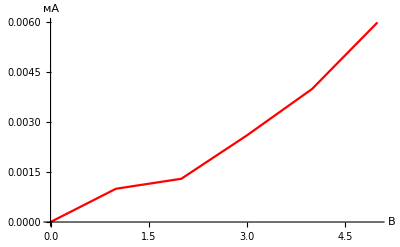

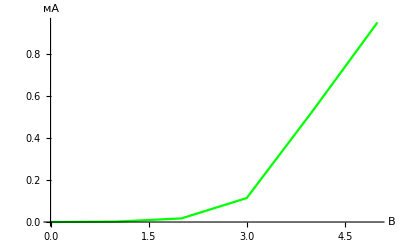

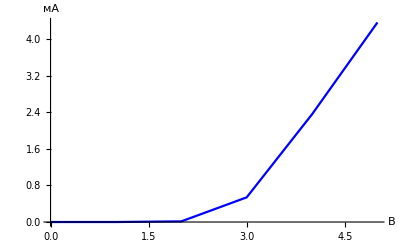

```mathematica
plot1 =ListLinePlot[VAH1, PlotStyle->Hue[1], AxesLabel->{В, мА}]
plot2 =ListLinePlot[VAH2, PlotStyle->RGBColor[0,255,0], AxesLabel->{В, мА}]
plot7 =ListLinePlot[VAH7, PlotStyle->RGBColor[0,0,255], AxesLabel->{В, мА}]
```

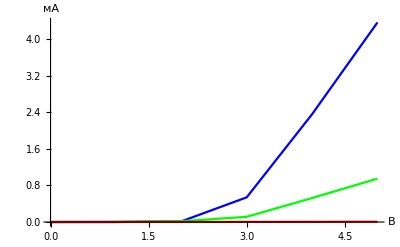

```mathematica
Show[plot7, plot2, plot1]
```